Solution for σ_∞ from equation A11

```mathematica
Solve[Subscript[σ, ∞]^2==λ^2 1/(1/Subscript[σ, ∞]^2+1/Subscript[σ, S]^2)+Subscript[σ, H]^2,Subscript[σ, ∞]]
```

{{σ_∞→-(√(σ_H^2-σ_S^2+λ^2 σ_S^2-√(4 σ_H^2 σ_S^2+(-σ_H^2+σ_S^2-λ^2 σ_S^2)^2)))/(√2)},{σ_∞→(√(σ_H^2-σ_S^2+λ^2 σ_S^2-√(4 σ_H^2 σ_S^2+(-σ_H^2+σ_S^2-λ^2 σ_S^2)^2)))/(√2)},{σ_∞→-(√(σ_H^2-σ_S^2+λ^2 σ_S^2+√(4 σ_H^2 σ_S^2+(-σ_H^2+σ_S^2-λ^2 σ_S^2)^2)))/(√2)},{σ_∞→(√(σ_H^2-σ_S^2+λ^2 σ_S^2+√(4 σ_H^2 σ_S^2+(-σ_H^2+σ_S^2-λ^2 σ_S^2)^2)))/(√2)}}

Simplification of the sum in equation A18

```mathematica
Sum[Sum[α^(t-n-k-1)a^n Subscript[b, k],{n,0,t-k-1}],{k,0,t-1}]
```

∑_(k=0)^(-1+t) -(a^-k α^-k (-a^t α^k+a^k α^t) b_k)/(a-α)

Sum the geometric series and taking the limit as t goes to ∞

```mathematica
Emtxt2=FullSimplify[(α-a)^-2  Sum[((ϵ-α+a)α^(t-k)-ϵ a^(t-k))^2 Subscript[σ, X]^2,{k,0,t}]]
```

((a^5 α (-1+α^(2+2 t))+2 a^(2+t) α^(3+t) ϵ-2 a^(4+t) α^(3+t) ϵ+2 a^(3+t) α^(2+t) (-1+α^2) ϵ-a^(2+2 t) (-1+α^2) ϵ^2+a^(3+2 t) α (-1+α^2) ϵ^2+a^4 (-(-1+α^(2+2 t)) (1+2 α (α-ϵ))+2 α (a α)^t ϵ)+α^2 (-1+α^(2 t) (α-ϵ)^2+2 α ϵ-ϵ^2)+a α (2+α^2-2 α^(2+2 t)-α^(4+2 t)-4 α ϵ+2 α^(1+2 t) ϵ+2 α^(3+2 t) ϵ-2 (a α)^t (-1+α^2) (α-ϵ) ϵ+2 ϵ^2-α^2 ϵ^2-α^(2+2 t) ϵ^2)+a^2 (-1+α^(4+2 t)-2 α^3 ϵ-2 α (-1+(a α)^t) ϵ-ϵ^2-α^(2+2 t) (-1+ϵ^2)+α^2 (-1+2 ϵ^2))+a^3 α (-1+α^(4+2 t)+4 α ϵ-2 α^(1+2 t) ϵ-2 α^(3+2 t) ϵ+(-1+2 (a α)^t) ϵ^2+α^(2+2 t) (1+ϵ^2)-α^2 (1+2 (a α)^t ϵ^2))) σ_X^2)/((-1+a^2) (a-α)^2 (-1+a α) (-1+α^2))

```mathematica
Limit[Emtxt2,t->Infinity]
```

Limit[((a^5 α (-1+α^(2+2 t))+2 a^(2+t) α^(3+t) ϵ-2 a^(4+t) α^(3+t) ϵ+2 a^(3+t) α^(2+t) (-1+α^2) ϵ-a^(2+2 t) (-1+α^2) ϵ^2+a^(3+2 t) α (-1+α^2) ϵ^2+a^4 (-(-1+α^(2+2 t)) (1+2 α (α-ϵ))+2 α (a α)^t ϵ)+α^2 (-1+α^(2 t) (α-ϵ)^2+2 α ϵ-ϵ^2)+a α (2+α^2-2 α^(2+2 t)-α^(4+2 t)-4 α ϵ+2 α^(1+2 t) ϵ+2 α^(3+2 t) ϵ-2 (a α)^t (-1+α^2) (α-ϵ) ϵ+2 ϵ^2-α^2 ϵ^2-α^(2+2 t) ϵ^2)+a^2 (-1+α^(4+2 t)-2 α^3 ϵ-2 α (-1+(a α)^t) ϵ-ϵ^2-α^(2+2 t) (-1+ϵ^2)+α^2 (-1+2 ϵ^2))+a^3 α (-1+α^(4+2 t)+4 α ϵ-2 α^(1+2 t) ϵ-2 α^(3+2 t) ϵ+(-1+2 (a α)^t) ϵ^2+α^(2+2 t) (1+ϵ^2)-α^2 (1+2 (a α)^t ϵ^2))) σ_X^2)/((-1+a^2) (a-α)^2 (-1+a α) (-1+α^2)),t→∞]

```mathematica
FullSimplify[Emtxt2/.t-> 100]
```

((-1+α^200 (α-ϵ)^2+2 α ϵ-ϵ^2) σ_X^2)/(-1+α^2)

```mathematica
Limit[((-1 + α^(2 t) (α - ϵ)^2 + 2 α ϵ - ϵ^2) Subscript[σ, X]^2)/(-1 + α^2),t->Infinity]
```

Limit[((-1+α^(2 t) (α-ϵ)^2+2 α ϵ-ϵ^2) σ_X^2)/(-1+α^2),t→∞]

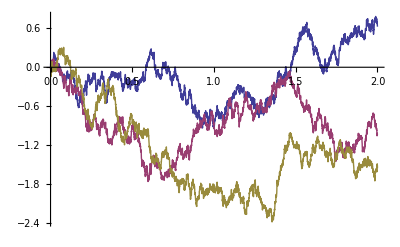

```mathematica
ListLinePlot[RandomFunction[WienerProcess[],{0,2,0.0005},3]]
```

```mathematica
path = RandomFunction[WienerProcess[],{0,1,0.1}]
```

TemporalData[1]

```mathematica
path["States"]
```

{{0.,0.219493,0.484051,0.491822,0.807597,0.902994,0.622702,0.576724,0.556226,1.2098,1.15122}}

```mathematica
Most[#].Differences[#]&/@%
```

{0.293286}